```mathematica
MyList[n_,p_]:=ReadList[StringJoin["d:\\Triangle\\Data\\",ToString[n], "\\",ToString[n],"_",ToString[p],".txt"],Number,2000]
```

```mathematica
MyCoordinateList[n_,p_] := Table[{ MyList[n,p][[i]], p},{i,1,2000}]
```

```mathematica
myGraph[range_, countLines_, maxRoot_] :=
Block[{},
minX =N[ range[[1]][[1]] ];
maxX =N[ range[[1]][[2]] ];
minY= N[ range[[2]][[1]] ];
maxY= N[ range[[2]][[2]] ];
log3 = If[maxRoot==0, IntegerPart[Ceiling[Log[3, maxX]]+1], maxRoot];
Show[
{
Table[
 Plot[{ (2 x/i)^j, (2x/(i +1))^j},{x,minX, maxX},
Filling->{1->{2}},
AxesLabel->{"n","p"}, 
PlotRange->range,
GridLines->{Table[k,{k,IntegerPart[Ceiling[minX]], IntegerPart[Floor [maxX]],1}],
Table[k,{k,IntegerPart[Ceiling[minY]], IntegerPart[Floor[maxY]],1}]
},
GridLinesStyle->Blue,
FillingStyle->Directive[Opacity[0.6],ColorData["DarkRainbow"][j]  ]
],
 {i,1,2*countLines,2},
  {j,Table[1/l,{l,1,log3   }] }]
}
]]
```

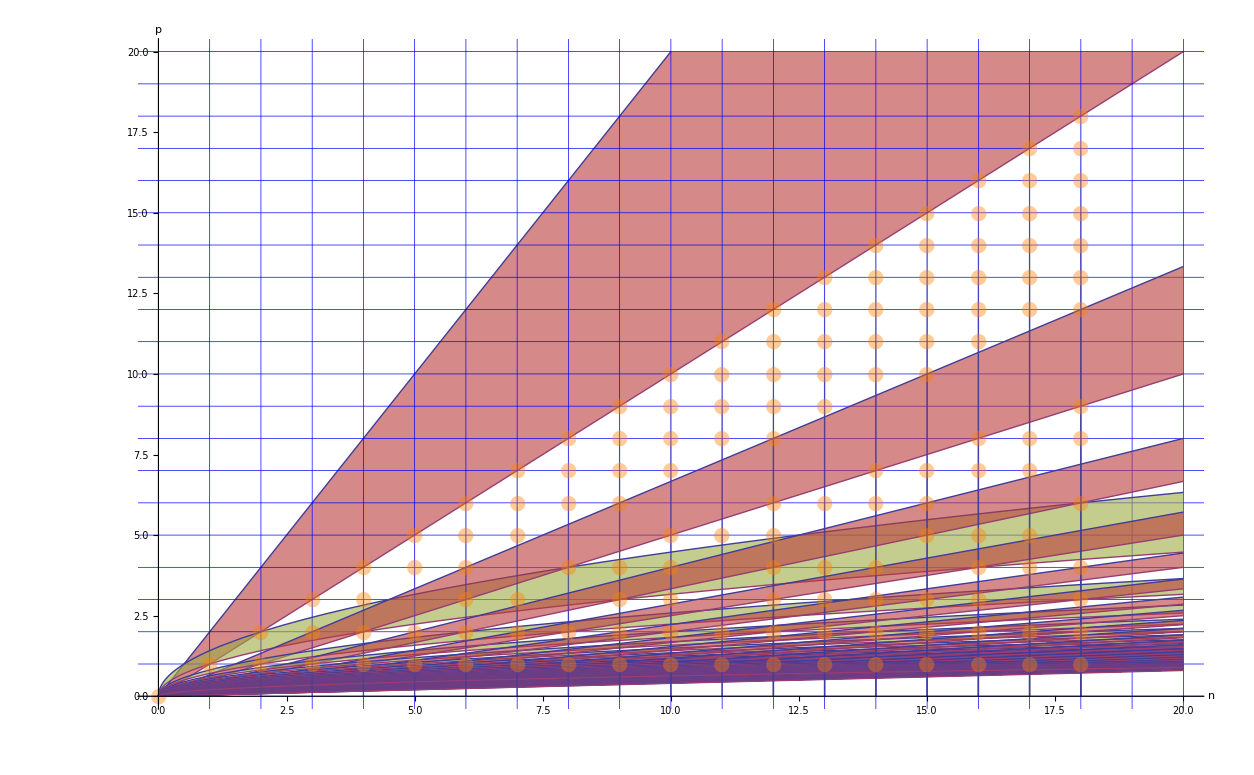

```mathematica
Block[
{myRange={{0,20},{0,20}} },
Show[myGraph[myRange, 50,2]
,
ListPlot[{{0,0},
                    {1,1},
                   {2,1}, {2,2},
                   {3,1}, {3,2},{3,3},
                    {4,1}, {4,2}, {4,3},{4,4},
                    {5,1},{5,2}, {5,4},{5,5},
                    {6,1}, {6,2},{6,3}, {6,4}, {6,5}, {6,6},
                    {7,1}, {7,2},{7,3}, {7,5}, {7,6}, {7,7},
                    {8,1}, {8,2},{8,4}, {8,6}, {8,7}, {8,8},
                    {9,1}, {9,2},{9,3},{9,4}, {9,6}, {9,7}, {9,8}, {9,9},
                   {10,1}, {10,2},{10,3},{10,4}, {10,5}, {10,7}, {10,8}, {10,9}, {10,10},
                   {11,1}, {11,2}, {11,5}, {11,8}, {11,9}, {11,10}, {11,11},
                   {12,1}, {12,2},{12,3},{12,4}, {12,5}, {12,6}, {12,8}, {12,9}, {12,10}, {12,11}, {12,12},
                   {13,1}, {13,2},{13,3},{13,4}, {13,6}, {13,9}, {13,10}, {13,11}, {13,12}, {13,13},
                   {14,1}, {14,2},{14,3},{14,4}, {14,6}, {14,7}, {14,10}, {14,11}, {14,12}, {14,13}, {14,14},
                   {15,1}, {15,2},{15,3},{15,5}, {15,6}, {15,7}, {15,10}, {15,11}, {15,12}, {15,13}, {15,14}, {15,15},
                   {16,1}, {16,2},{16,3},{16,4},{16,5}, {16,7}, {16,8}, {16,11}, {16,12}, {16,13}, {16,14}, {16,15}, {16,16},
                   {17,1}, {17,2},{17,4},{17,5}, {17,7}, {17,8}, {17,12}, {17,13}, {17,14}, {17,15}, {17,16}, {17,17},
                   {18,1}, {18,2}, {18,3},{18,4},{18,6}, {18,8}, {18,9}, {18,12}, {18,13}, {18,14}, {18,15}, {18,16}, {18,17}, {18,18}
},
PlotMarkers->{Automatic,20},
PlotStyle->Directive[Opacity[0.4], Orange],
PlotRange->myRange,  
Filling->Axis]]
]
```

```mathematica
FromDigits[{1,1,0,1,1},3]
```

112

```mathematica
Solve[{A==w+1/2 B - 1} , {w}]
```

{{w→1/2 (2+2 A-B)}}

```mathematica
Solve[{B==2 (1+A-w), w==1/2 (2+2 A-B)},{B,w}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{B→2 (1+A)-2 w}}

FromDigits::nlst: The expression 1 is not a list of digits or a string of valid digits.

FromDigits[1,2]

```mathematica
sums = Table[Length[Select[{{1,1},
                   {2,1}, {2,2},
                   {3,1}, {3,2},{3,3},
                    {4,1}, {4,2}, {4,3},{4,4},
                    {5,1},{5,2}, {5,4},{5,5},
                    {6,1}, {6,2},{6,3}, {6,4}, {6,5}, {6,6},
                    {7,1}, {7,2},{7,3}, {7,5}, {7,6}, {7,7},
                    {8,1}, {8,2},{8,4}, {8,6}, {8,7}, {8,8},
                    {9,1}, {9,2},{9,3},{9,4}, {9,6}, {9,7}, {9,8}, {9,9},
                   {10,1}, {10,2},{10,3},{10,4}, {10,5}, {10,7}, {10,8}, {10,9}, {10,10},
                   {11,1}, {11,2}, {11,5}, {11,8}, {11,9}, {11,10}, {11,11},
                   {12,1}, {12,2},{12,3},{12,4}, {12,5}, {12,6}, {12,8}, {12,9}, {12,10}, {12,11}, {12,12},
                   {13,1}, {13,2},{13,3},{13,4}, {13,6}, {13,9}, {13,10}, {13,11}, {13,12}, {13,13},
                   {14,1}, {14,2},{14,3},{14,4}, {14,6}, {14,7}, {14,10}, {14,11}, {14,12}, {14,13}, {14,14},
                   {15,1}, {15,2},{15,3},{15,5}, {15,6}, {15,7}, {15,10}, {15,11}, {15,12}, {15,13}, {15,14}, {15,15},
                   {16,1}, {16,2},{16,3},{16,4},{16,5}, {16,7}, {16,8}, {16,11}, {16,12}, {16,13}, {16,14}, {16,15}, {16,16},
                   {17,1}, {17,2},{17,4},{17,5}, {17,7}, {17,8}, {17,12}, {17,13}, {17,14}, {17,15}, {17,16}, {17,17},
                   {18,1}, {18,2}, {18,3},{18,4},{18,6}, {18,8}, {18,9}, {18,12}, {18,13}, {18,14}, {18,15}, {18,16}, {18,17}, {18,18}
}, #[[1]]==n &]], {n,0,18}]
```

{0,1,2,3,4,4,6,6,6,8,9,7,11,10,11,12,13,12,14}

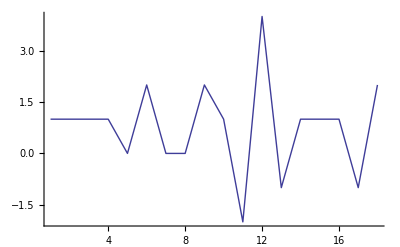

```mathematica
ListPlot[sums, Joined->True]
```

```mathematica
Block[
{j=1},
Table[{ (2 x/i), (2x/(i +1))},{i,0,k},  {k,0,10}, {l,0,10}]
]
```

Table::iterb: Iterator {i, 0, k} does not have appropriate bounds.

```mathematica
LowerCouples[bound_]:=Flatten[Table[{i,j},{i,1,bound},{j,1,i}],1]
```

```mathematica
LowerCouples[3]
```

{{1,1},{2,1},{2,2},{3,1},{3,2},{3,3}}

```mathematica
myCalc[n_] := Block[{result},
result = {};
Do[ x = couple[[1]];
      y = couple[[2]];
      Do [
             If[2x/(i +1)>= y >= 2x / (i+2),
                 result = Append[result, {x,y}]
                (*Print[{"OK",2x/(i +1), {x,y} , 2x / (i+2)}]*)
(*,
               Print[{"Not",2x/(i +1), {x,y} , 2x / (i+2)}]*)
         ]
         , {i,1,x*2,2}
     ];
      result;
   , {couple, LowerCouples[n]}
];
result 
]
```

```mathematica
Length[myCalc[18]]
```

138

```mathematica
Block[
 {myRange = {{0, 10}, {0, 10}} },
 Show[myGraph[myRange, 4, 1]
  ,
  ListPlot[myCalc[myRange[[1]][[2]] ],
   PlotMarkers -> {Automatic, 20},
   PlotStyle -> Directive[Opacity[0.4], Orange],
   PlotRange -> myRange,  
   Filling -> Axis]]
 ]
```

ListPlot::lpn: myCalc[10] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[myGraph[{{0, 10}, {0, 10}}, 4, 1], ListPlot[myCalc[10], PlotMarkers → {Automatic, 20}, PlotStyle → Directive[Opacity[0.4`], RGBColor[1, 0.5`, 0]], PlotRange → {{0, 10}, {0, 10}}, Filling → Axis]].

ListPlot::lpn: myCalc[10] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

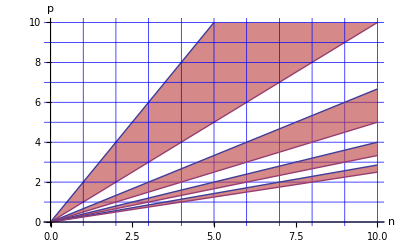
Show[-Graphics-,ListPlot[myCalc[10],PlotMarkers→{Automatic,20},PlotStyle→Directive[Opacity[0.4],RGBColor[1,0.5,0]],PlotRange→{{0,10},{0,10}},Filling→Axis]]

```mathematica
Show[myGraph[{{0,10},{0,10}},4,1],ListPlot[myCalc[10],PlotMarkers->{Automatic,20},PlotStyle->Directive[Opacity[0.4],RGBColor[1,0.5,0]],PlotRange->{{0,10},{0,10}},Filling->Axis]]
```

```mathematica
myCalcOnly[n_,power_] := Block[{result,x},
result = {};
x=n;
Do[ 
 Do [
             If[(2x/(i +1))^(1/power)>= y >= (2x / (i+2))^(1/power),
                 result = Append[result, {x,y}]
                (*Print[{"OK",2x/(i +1), {x,y} , 2x / (i+2)}]*)
(*,
               Print[{"Not",2x/(i +1), {x,y} , 2x / (i+2)}]*)
         ]
         , {i,1,IntegerPart[Ceiling[(x*2)^(1/power)]],2}
     ];
      result;
   , {y, 1,IntegerPart[x^(1/power)]}
];
result 
]
```

```mathematica
myCalcCount[n_,power_] := Block[{result,x},
result = 0;
x=n;
Do[ 
 Do [
             If[(2x/(i +1))^(1/power)>= y >= (2x / (i+2))^(1/power),
                 result = result+1;
                (*Print[{"OK",2x/(i +1), {x,y} , 2x / (i+2)}]*)
(*,
               Print[{"Not",2x/(i +1), {x,y} , 2x / (i+2)}]*)
         ]
         , {i,1,IntegerPart[Ceiling[(x*2)^(1/power)]],2}
     ];
      result;
   , {y, 1,IntegerPart[x^(1/power)]}
];
result 
]
```

```mathematica
Sort[Flatten[Table[myCalcOnly[3610,n],{n,1,20}],1]]
```

$Aborted

```mathematica
Differences[Table[Length[myCalcOnly[n,1]],{n,1,100}]]
```

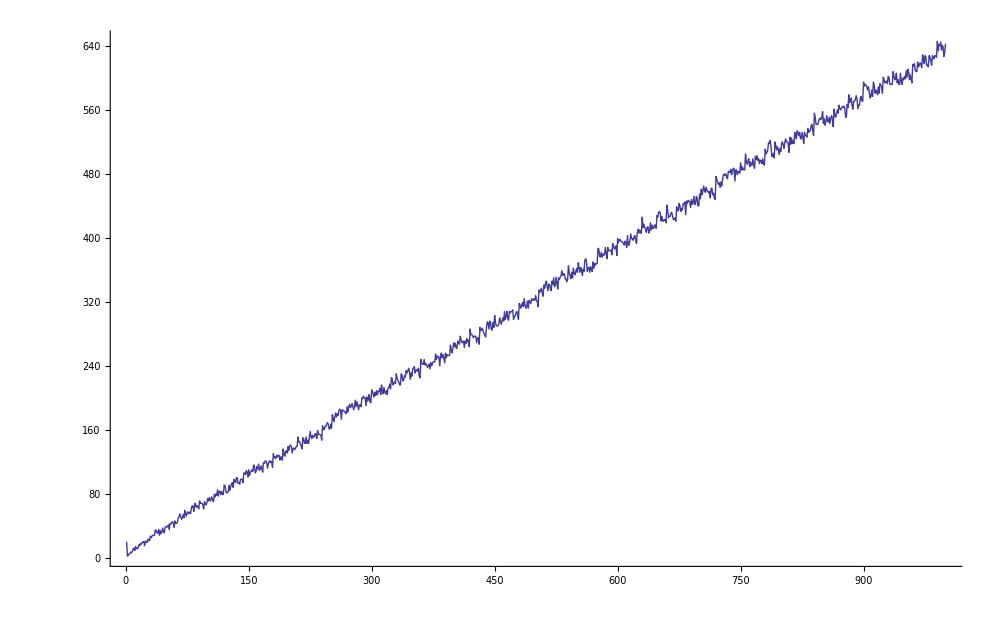

```mathematica
ListPlot[Table[Sum[myCalcCount[n,i],{i,1,20}],{n,1,1000}],Joined->True ]
```

```mathematica
myCalcOnlyBis[n_,i_] := Block[{result},
result = {};
Do[ 

             If[2x/(i +1)>= y >= 2x / (i+2),
                 result = Append[result, {x,y}]
                (*Print[{"OK",2x/(i +1), {x,y} , 2x / (i+2)}]*)
(*,
               Print[{"Not",2x/(i +1), {x,y} , 2x / (i+2)}]*)
        
     ];
      result;
   , {x,n,n},{y, 1,x}
];
result 
]
```

```mathematica
En dan gaan we nu vergelijkingen opstellen.  Eerst een tabel met de lineaire vergelijkingen
```

```mathematica
Table[{(2 x/(i+1)), (2x/(i +2))}, {i,1,10,2}]
```

{{x,(2 x)/3},{x/2,(2 x)/5},{x/3,(2 x)/7},{x/4,(2 x)/9},{x/5,(2 x)/11}}

```mathematica
Aantal lattice points onder of op de rechte y=x
```

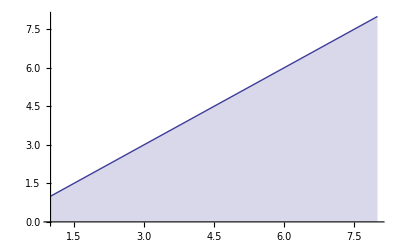

```mathematica
ListPlot[Table[{x,x},{x,1,8}], Joined->True, Filling->Axis, PlotRange->{All,{0,8}}]
```

```mathematica
Aantal laatice punten volledig onder of op rechte y=2/3x
```

Set::write: Tag Times in Aantal laatice of onder op punten rechte volledig y is Protected.

(2 x)/3

```mathematica
Table[{x,Floor[((x)*2)/3]},{x,1,8}]
```

{{1,0},{2,1},{3,2},{4,2},{5,3},{6,4},{7,4},{8,5}}

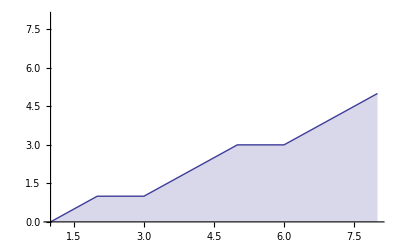

```mathematica
ListPlot[Table[{x,Floor[((x)*2)/3]- If[Floor[((x)*2)/3]== ((x)*2)/3,1,0]},{x,1,8}], Joined->True, Filling->Axis, PlotRange->{All,{0,8}}]
```

```mathematica
Aantal lattice points tussen echte y=x en rechte y=2/3x
```

```mathematica
Table[Sum[Floor[((x)*2)/(i+1)] -(Floor[((x)*2)/(i+2)]- If[Floor[((x)*2)/(i+2)]== ((x)*2)/(i+2),1,0]),{i,1,x,2}],{x,1,8}]
```

{1,1,2,3,3,5,5,5}

```mathematica
Table[Table[Floor[((x)*2)/(i+1)] -Floor[((x)*2)/(i+2)],{i,1,2*x,2}],{x,1,8}](*, Joined->True, Filling->Axis, PlotRange->{All,{0,8}}]*)
```

{{1},{1,1},{1,0,1},{2,1,0,1},{2,0,0,0,1},{2,1,1,0,0,1},{3,1,0,0,0,0,1},{3,1,0,1,0,0,0,1}}